```mathematica
x[t_] := Cos[t]
snapshots = Table[x[Pi*RandomReal[j]],{j, 10000}]
```

{0.969173,0.791814,-0.782467,-0.994286,-0.973129,0.505617,0.568374,0.0140705,-0.457203,0.0615988,0.330436,9978,0.949673,0.837533,-0.157537,0.778176,-0.888629,-0.69679,-0.288738,0.951617,-0.631918,0.999858,-0.994894}
 |  |  |  |

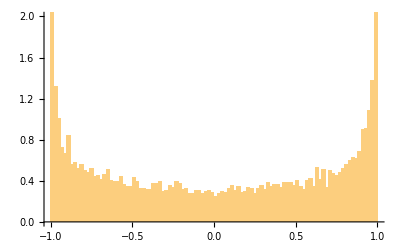

```mathematica
Histogram[snapshots,100,"PDF", PlotRange->{0,2}]
```